```mathematica
data = Import["~/zeca-analise/join_count_acertos.csv"];
```

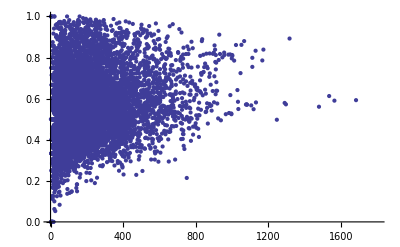

```mathematica
ListPlot[data[[All,{2,5}]], PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic"]
```

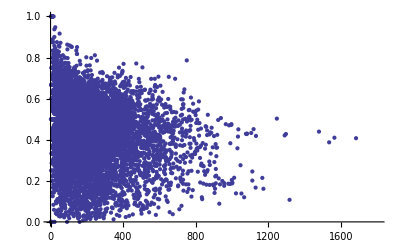

```mathematica
ListPlot[data[[All,{2,6}]], PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic"]
```

```mathematica
Correlation[data[[All,2]],data[[All,5]]]
```

0.208672

```mathematica
dataH = Import["~/zeca-analise/join_count_acertos_h.csv"];
```

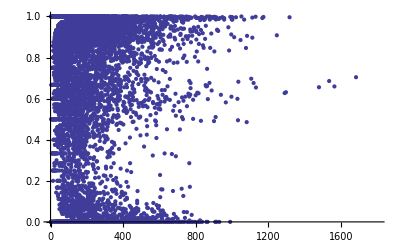

```mathematica
ListPlot[dataH[[All,{2,5}]], PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic"]
```

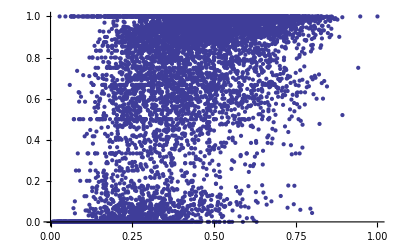

```mathematica
ListPlot[dataH[[All,{7,5}]], PlotRange->{{0,1},{0,1}}, PlotTheme->"Classic"]
```

```mathematica
ListPointPlot3D[dataH[[All,{2,7,5}]], PlotRange->{{0,1800},{0,1},{0,1}}, AxesLabel->{"Frequencia", "Fracao", "Acertos"}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
ListPointPlot3D[dataH[[All,{8,7,5}]], PlotRange->{{0,1300},{0,1},{0,1}}, AxesLabel->{"Frequencia", "Fracao", "Acertos"}, ColorFunction->"Rainbow"]
```

-Graphics3D-

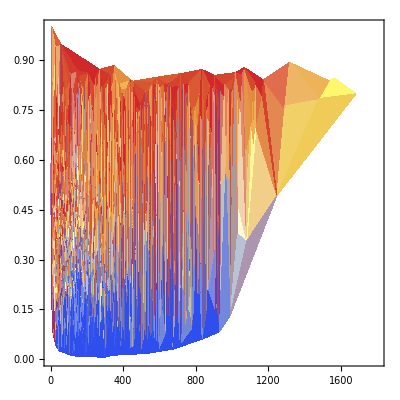

```mathematica
ListDensityPlot[dataH[[All,{2,7,5}]],InterpolationOrder->1, PlotRange->{{0,1800},{0,1},{0,1}},ColorFunction->"Temperature"]
```

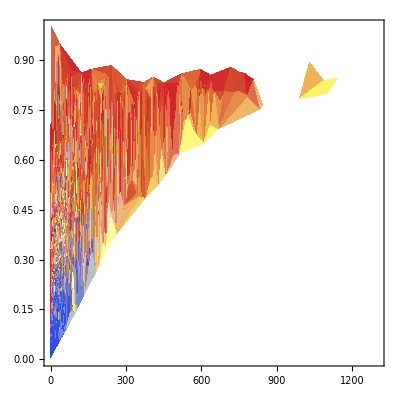

```mathematica
ListDensityPlot[dataH[[All,{8,7,5}]],InterpolationOrder->1, PlotRange->{{0,1300},{0,1},{0,1}},ColorFunction->"Temperature"]
```

```mathematica
Correlation[dataH[[All,2]],dataH[[All,5]]]
```

-0.0455421

```mathematica
Correlation[dataH[[All,7]],dataH[[All,5]]]
```

0.614328

```mathematica
Correlation[dataH[[All,8]],dataH[[All,5]]]
```

0.257814

```mathematica
dataE = Import["~/zeca-analise/join_count_acertos_e.csv"];
```

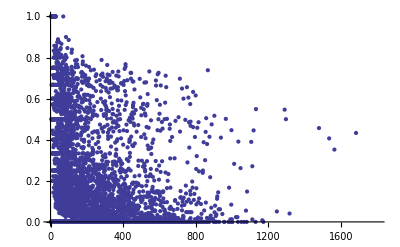

```mathematica
ListPlot[dataE[[All,{2,5}]], PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic"]
```

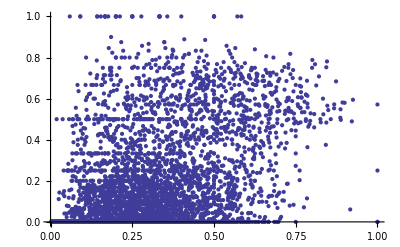

```mathematica
ListPlot[dataE[[All,{7,5}]], PlotRange->{{0,1},{0,1}}, PlotTheme->"Classic"]
```

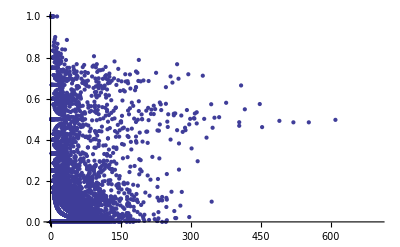

```mathematica
ListPlot[dataE[[All,{8,5}]], PlotRange->{{0,700},{0,1}}, PlotTheme->"Classic"]
```

```mathematica
ListPointPlot3D[dataE[[All,{2,7,5}]], PlotRange->{{0,1800},{0,1},{0,1}}, AxesLabel->{"Frequencia", "Fracao", "Acertos"}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
ListPointPlot3D[dataE[[All,{8,7,5}]], PlotRange->{{0,800},{0,1},{0,1}}, AxesLabel->{"Frequencia", "Fracao", "Acertos"}, ColorFunction->"Rainbow"]
```

-Graphics3D-

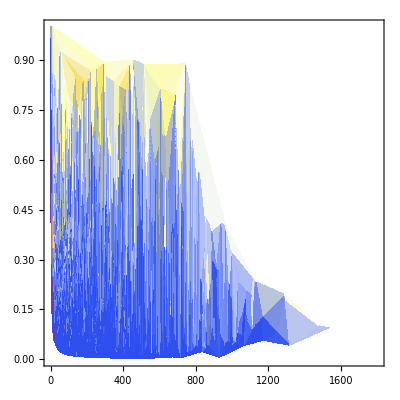

```mathematica
ListDensityPlot[dataE[[All,{2,7,5}]], PlotRange->{{0,1800},{0,1},{0,1}},ColorFunction->"TemperatureMap"]
```

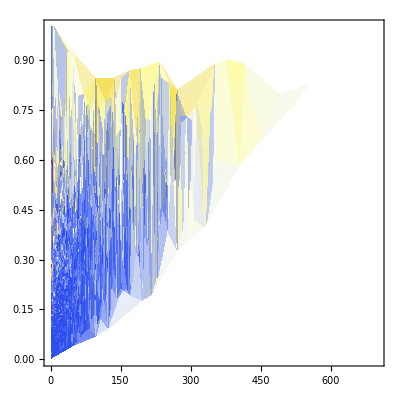

```mathematica
ListDensityPlot[dataE[[All,{8,7,5}]], PlotRange->{{0,700},{0,1},{0,1}},ColorFunction->"TemperatureMap"]
```

```mathematica
Correlation[dataE[[All,2]],dataE[[All,5]]]
```

-0.0939965

```mathematica
Correlation[dataE[[All,7]],dataE[[All,5]]]
```

0.531294

```mathematica
Correlation[dataE[[All,8]],dataE[[All,5]]]
```

0.255789

```mathematica
dataC = Import["~/zeca-analise/join_count_acertos_c.csv"];
```

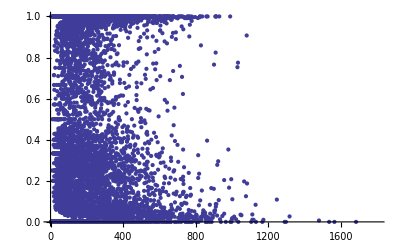

```mathematica
ListPlot[dataC[[All,{2,5}]], PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic"]
```

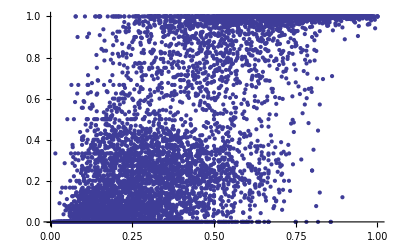

```mathematica
ListPlot[dataC[[All,{7,5}]], PlotRange->{{0,1},{0,1}}, PlotTheme->"Classic"]
```

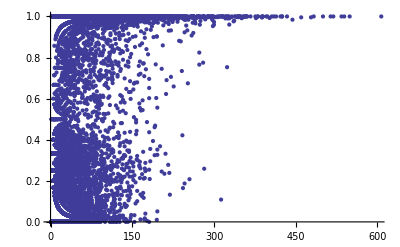

```mathematica
ListPlot[dataC[[All,{8,5}]], PlotRange->{{0,600},{0,1}}, PlotTheme->"Classic"]
```

```mathematica
ListPointPlot3D[dataC[[All,{2,7,5}]], PlotRange->{{0,1800},{0,1},{0,1}}, AxesLabel->{"Frequencia", "Fracao", "Acertos"}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
ListPointPlot3D[dataC[[All,{8,7,5}]], PlotRange->{{0,600},{0,1},{0,1}}, AxesLabel->{"Frequencia", "Fracao", "Acertos"}, ColorFunction->"Rainbow"]
```

-Graphics3D-

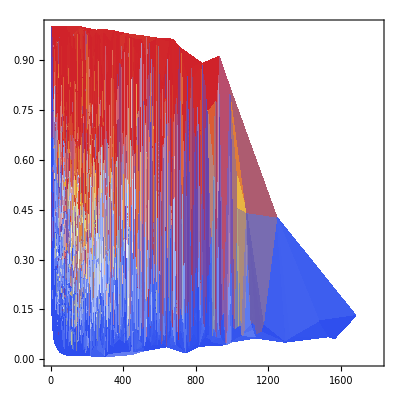

```mathematica
ListDensityPlot[dataC[[All,{2,7,5}]], PlotRange->{{0,1800},{0,1},{0,1}},ColorFunction->"TemperatureMap"]
```

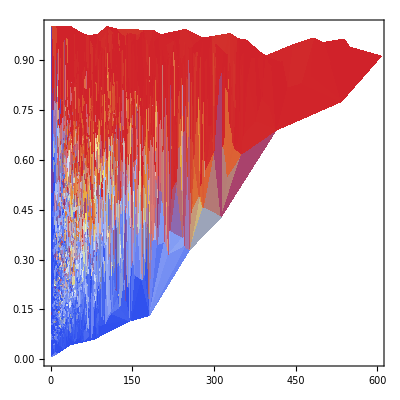

```mathematica
ListDensityPlot[dataC[[All,{8,7,5}]], PlotRange->{{0,600},{0,1},{0,1}},ColorFunction->"TemperatureMap"]
```

```mathematica
Correlation[dataC[[All,2]],dataC[[All,5]]]
```

0.0641282

```mathematica
Correlation[dataC[[All,7]],dataC[[All,5]]]
```

0.776096

```mathematica
Correlation[dataC[[All,8]],dataC[[All,5]]]
```

0.51075